Bias = (1/2, -Log[3]/2), weight = Log[3]. The stable fixed points are 0 and 1, the unstable fixed point is 1/2. The function returns almost exactly its argument.

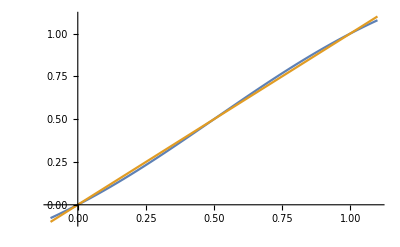

```mathematica
Plot[{Tanh[Log[3](x - 1/2)] + 1/2, x}, {x, -0.1, 1.1}]
```

Generate a “step-like” function:

Bias = {0.99999,-6.10303};    weight = 6.10309

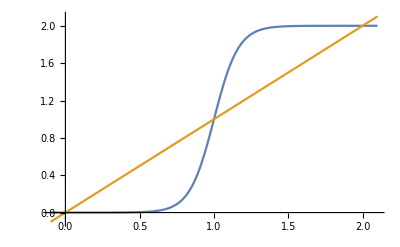

```mathematica
Block[{k = 1 - 10^-5, a}, a = 1/k ArcTanh[k]; Print[Row[{"Bias = ", N@{k, -a*k}, ";    weight = ", N@a}]];   Plot[{Tanh[a(x-k)] + k, x}, {x, -0.1, 2*k+0.1}]]
```

Approximate this with a simpler function:

Bias = {1.,-10.};    weight = 10.

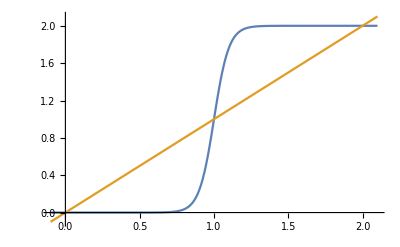

```mathematica
Block[{a = 10}, Print[Row[{"Bias = ", N@{1, -a}, ";    weight = ", N@a}]];   Plot[{Tanh[a(x-1)] + 1, x}, {x, -0.1, 2+0.1}]]
```